# SI Brochure Data

This data contains data from the SI Brochure published by the BIPM

### Details

We recommend using shorter key terms formatted with CamelCase if they are  and having a table in the Details section; e.g.,

"BaseQuantities" -> "base quantities and units"

Do I need to replace all keys like hyperfine-transition-frequency-of-Cs as HyperfineTransitionFrequencyOfCs? I want to make sure I understand the issue.

As a general matter, we recommend using CamelCase (e.g. HyperfineTransitionFrequencyOfCs) for a good balance of readability and conciseness. If you would prefer to keep your keys as they are they're OK, but we recommend this style to all submitters.

I think I don't want to go through the work of renaming all the keys so I'm going to leave it as it is. I based on the naming convention for GitHub repositories.

## Data Definitions

### Primary Content

```mathematica
ResourceData[{{}}]=Dataset[<|"hyperfine-transition-frequency-of-Cs"-><|"numerical-value"->9192631770,"unit"->"Hz"|>,"speed-of-light-in-vacuum"-><|"numerical-value"->299792458,"unit"->"m s^-1"|>,"Planck-constant"-><|"numerical-value"->6.62607015 10^-34,"unit"->"J s"|>,"elementary-charge"-><|"numerical-value"->1.602176634 10^-19,"unit"->"C"|>,"Boltzmann-constant"-><|"numerical-value"->1.380649 10^-23,"unit"->"J K^-1"|>,"Avogadro-constant"-><|"numerical-value"->6.02214076 10^23,"unit"->"mol^-1"|>,"luminous-efficacy"-><|"numerical-value"->683,"unit"->"lm W^-1"|>|>]
```

### Additional Data Elements (optional)

```mathematica
ResourceData[{{}},"defining-constants-of-the-SI"]=Dataset[<|"hyperfine-transition-frequency-of-Cs"-><|"numerical-value"->9192631770,"unit"->"Hz"|>,"speed-of-light-in-vacuum"-><|"numerical-value"->299792458,"unit"->"m s^-1"|>,"Planck-constant"-><|"numerical-value"->6.62607015 10^-34,"unit"->"J s"|>,"elementary-charge"-><|"numerical-value"->1.602176634 10^-19,"unit"->"C"|>,"Boltzmann-constant"-><|"numerical-value"->1.380649 10^-23,"unit"->"J K^-1"|>,"Avogadro-constant"-><|"numerical-value"->6.02214076 10^23,"unit"->"mol^-1"|>,"luminous-efficacy"-><|"numerical-value"->683,"unit"->"lm W^-1"|>|>]
```

```mathematica
ResourceData[{{}},"base-quantities-and-units"]=Dataset[<|"time"-><|"quantity-name"->"time","typical-quantity-symbol"->"t","unit-name"->"second","unit-symbol"->"s"|>,"length"-><|"quantity-name"->"length","typical-quantity-symbol"->"l","unit-name"->"meter","unit-symbol"->"m"|>,"mass"-><|"quantity-name"->"mass","typical-quantity-symbol"->"l","unit-name"->"kilogram","unit-symbol"->"kg"|>,"electric-current"-><|"quantity-name"->"electric-current","typical-quantity-symbol"->"i","unit-name"->"ampere","unit-symbol"->"A"|>,"thermodynamic-temperature"-><|"quantity-name"->"thermodynamic-temperature","typical-quantity-symbol"->"T","unit-name"->"kelvin","unit-symbol"->"K"|>,"amount-of-substance"-><|"quantity-name"->"amount-of-substance","typical-quantity-symbol"->"n","unit-name"->"mole","unit-symbol"->"mol"|>,"luminous-intensity"-><|"quantity-name"->"luminous-intensity","typical-quantity-symbol"->"I_v","unit-name"->"candela","unit-symbol"->"cd"|>|>]
```

```mathematica
ResourceData[{{}},"base-quantities-and-dimensions"]=Dataset[<|"time"-><|"typical-symbol-for-quantity"->"t","symbol-for-dimension"->"T"|>,"length"-><|"typical-symbol-for-quantity"->"l","symbol-for-dimension"->"L"|>,"mass"-><|"typical-symbol-for-quantity"->"m","symbol-for-dimension"->"M"|>,"electric-current"-><|"typical-symbol-for-quantity"->"i","symbol-for-dimension"->"I"|>,"thermodynamic-temperature"-><|"typical-symbol-for-quantity"->"T","symbol-for-dimension"->"Θ"|>,"amount-of-substance"-><|"typical-symbol-for-quantity"->"n","symbol-for-dimension"->"N"|>,"luminous-intensity"-><|"typical-symbol-for-quantity"->"I_v","symbol-for-dimension"->"J"|>|>]
```

```mathematica
ResourceData[{{}},"SI-units-with-special-names-and-symbols"]=Dataset[<|"plane-angle"-><|"special-name-of-unit"->"radian","unit-expressed-terms-of-base-units"->"rad=m/m","unit-expressed-in-terms-of-other-SI-units"->""|>,"solid-angle"-><|"special-name-of-unit"->"steradian","unit-expressed-terms-of-base-units"->"sr=m^2/m^2","unit-expressed-in-terms-of-other-SI-units"->""|>,"frequency"-><|"special-name-of-unit"->"hertz","unit-expressed-terms-of-base-units"->"Hz=s^-1","unit-expressed-in-terms-of-other-SI-units"->""|>,"force"-><|"special-name-of-unit"->"newton","unit-expressed-terms-of-base-units"->"N=kg m s^-2","unit-expressed-in-terms-of-other-SI-units"->""|>,"pressure-or-stress"-><|"special-name-of-unit"->"pascal","unit-expressed-terms-of-base-units"->"Pa=kg m^-1 s^-2","unit-expressed-in-terms-of-other-SI-units"->""|>,"energy-or-work-or-amount-of-heat"-><|"special-name-of-unit"->"joule","unit-expressed-terms-of-base-units"->"J=kg m^2 s^-2","unit-expressed-in-terms-of-other-SI-units"->"N m"|>,"power-or-radiant-flux"-><|"special-name-of-unit"->"watt","unit-expressed-terms-of-base-units"->"W=kg m^2 s^-3","unit-expressed-in-terms-of-other-SI-units"->"J/s"|>,
"electric-charge"-><|"special-name-of-unit"->"coulomb","unit-expressed-terms-of-base-units"->"C=A s","unit-expressed-in-terms-of-other-SI-units"->""|>,
"electric-potential-difference"-><|"special-name-of-unit"->"volt","unit-expressed-terms-of-base-units"->"V=kg m^2 s^-3 A^-1","unit-expressed-in-terms-of-other-SI-units"->"W/A"|>,
"capacitance"-><|"special-name-of-unit"->"farad","unit-expressed-terms-of-base-units"->"F=kg^-1 m^-2 s^4 A^2","unit-expressed-in-terms-of-other-SI-units"->"C/V"|>,
"electric-resistance"-><|"special-name-of-unit"->"ohm","unit-expressed-terms-of-base-units"->"Ω=kg m^2 s^-3 A^-2","unit-expressed-in-terms-of-other-SI-units"->"V/A"|>,
"electric-conductance"-><|"special-name-of-unit"->"siemens","unit-expressed-terms-of-base-units"->"S=kg^-1 m^-2 s^3 A^2","unit-expressed-in-terms-of-other-SI-units"->"A/V"|>,
"magnetic-flux"-><|"special-name-of-unit"->"weber","unit-expressed-terms-of-base-units"->"Wb=kg m^2 s^-2 A^-1","unit-expressed-in-terms-of-other-SI-units"->"V s"|>,
"magnetic-flux-density"-><|"special-name-of-unit"->"tesla","unit-expressed-terms-of-base-units"->"T=kg s^-2 A^-1","unit-expressed-in-terms-of-other-SI-units"->"Wb/m^2"|>,
"inductance"-><|"special-name-of-unit"->"henry","unit-expressed-terms-of-base-units"->"H=kg m^2 s^-2 A^-2","unit-expressed-in-terms-of-other-SI-units"->"Wb/A"|>,"Celsius-temperature"-><|"special-name-of-unit"->"degree Celsius","unit-expressed-terms-of-base-units"->"°C=K","unit-expressed-in-terms-of-other-SI-units"->""|>,"luminous-flux"-><|"special-name-of-unit"->"lumen","unit-expressed-terms-of-base-units"->"lm=cd sr","unit-expressed-in-terms-of-other-SI-units"->""|>,"illuminance"-><|"special-name-of-unit"->"lux","unit-expressed-terms-of-base-units"->"lx=cd sr m^-2","unit-expressed-in-terms-of-other-SI-units"->"lm/m^2"|>,"activity-referred-to-a-radionuclide"-><|"special-name-of-unit"->"becquerel","unit-expressed-terms-of-base-units"->"Bq=s^-1","unit-expressed-in-terms-of-other-SI-units"->""|>,"absorbed-dose-or-kerma"-><|"special-name-of-unit"->"gray","unit-expressed-terms-of-base-units"->"Gy=m^2 s^-2","unit-expressed-in-terms-of-other-SI-units"->"J/kg"|>,"dose-equivalent"-><|"special-name-of-unit"->"sievert","unit-expressed-terms-of-base-units"->"Sv=m^2 s^-2","unit-expressed-in-terms-of-other-SI-units"->"J/kg"|>,"catalytic-activity"-><|"special-name-of-unit"->"katal","unit-expressed-terms-of-base-units"->"kat=mol s^-1","unit-expressed-in-terms-of-other-SI-units"->""|>|>]
```

```mathematica
ResourceData[{{}},"coherent-derived-units-in-the-SI-expressed-terms-of-base-units"]=Dataset[<|"area"-><|"typical-symbol"->"A","derived-unit-expressed-in-terms-of-base-units"->"m^2"|>,
"volume"-><|"typical-symbol"->"V","derived-unit-expressed-in-terms-of-base-units"->"m^3"|>,"speed-or-velocity"-><|"typical-symbol"->"v","derived-unit-expressed-in-terms-of-base-units"->"m s^-1"|>,"acceleration"-><|"typical-symbol"->"a","derived-unit-expressed-in-terms-of-base-units"->"m s^-2"|>,"wavenumber"-><|"typical-symbol"->"σ","derived-unit-expressed-in-terms-of-base-units"->"m^-1"|>,"density-or-mass-density"-><|"typical-symbol"->"ρ","derived-unit-expressed-in-terms-of-base-units"->"kg m^-3"|>,"surface-density"-><|"typical-symbol"->"ρ_A","derived-unit-expressed-in-terms-of-base-units"->"kg m^-2"|>,"specific-volume"-><|"typical-symbol"->"ν","derived-unit-expressed-in-terms-of-base-units"->"m^3 kg^-1"|>,"current-density"-><|"typical-symbol"->"j","derived-unit-expressed-in-terms-of-base-units"->"A m^-2"|>,"magnetic-field-strength"-><|"typical-symbol"->"H","derived-unit-expressed-in-terms-of-base-units"->"A m^-1"|>,"amount-of-substance-concentration"-><|"typical-symbol"->"c","derived-unit-expressed-in-terms-of-base-units"->"mol m^-3"|>,"mass-concentration"-><|"typical-symbol"->"ρ-or-γ","derived-unit-expressed-in-terms-of-base-units"->"kg m^-3"|>,"luminance"-><|"typical-symbol"->"L_v","derived-unit-expressed-in-terms-of-base-units"->"cd m^-2"|>|>]
```

```mathematica
ResourceData[{{}},"coherent-derived-units-whose-names-and-symbols-include-SI-coherent-derived-units-with-special-names-and-symbols"]=Dataset[<|"dynamic-viscosity"-><|"name-of-coherent-derived-unit"->"pascal second","symbol"->"Pa s","derived-unit-expressed-in-terms-of-base-units"->"kg m^-1 s^-1"|>,
"moment-of-force"-><|"name-of-coherent-derived-unit"->"newton meter","symbol"->"N m","derived-unit-expressed-in-terms-of-base-units"->"kg m^2 s^-2"|>,"surface-tension"-><|"name-of-coherent-derived-unit"->"newton per meter","symbol"->"N m^-1","derived-unit-expressed-in-terms-of-base-units"->"kg s^-2"|>,"angular-velocity-or-angular-frequency"-><|"name-of-coherent-derived-unit"->"radian per second","symbol"->"rad s^-1","derived-unit-expressed-in-terms-of-base-units"->"s^-1"|>,"angular-acceleration"-><|"name-of-coherent-derived-unit"->"radian per second squared","symbol"->"rad/s^2","derived-unit-expressed-in-terms-of-base-units"->"s^-2"|>,"heat-flux-density-or-irradiance"-><|"name-of-coherent-derived-unit"->"watt per square meter","symbol"->"W/m^2","derived-unit-expressed-in-terms-of-base-units"->"kg s^-3"|>,"heat-capacity-or-entropy"-><|"name-of-coherent-derived-unit"->"joule per kelvin","symbol"->"J K^-1","derived-unit-expressed-in-terms-of-base-units"->"kg m^2 s^-2 K^-1"|>,"specific-heat-capacity-or-specific-entropy"-><|"name-of-coherent-derived-unit"->"joule per kilogram kelvin","symbol"->"J K^-1 kg^-1","derived-unit-expressed-in-terms-of-base-units"->"m^2 s^-2 K^-1"|>,"specific-energy"-><|"name-of-coherent-derived-unit"->"joule per kilogram","symbol"->"J kg^-1","derived-unit-expressed-in-terms-of-base-units"->"m^2 s^-2"|>,"thermal-conductivity"-><|"name-of-coherent-derived-unit"->"watt per meter kelvin","symbol"->"W m^-1 K^-1","derived-unit-expressed-in-terms-of-base-units"->"kg m s^-3 K^-1"|>,"energy-density"-><|"name-of-coherent-derived-unit"->"joule per cubic meter","symbol"->"J m^-3","derived-unit-expressed-in-terms-of-base-units"->"kg m^-1 s^-2"|>,"electric-field-strength"-><|"name-of-coherent-derived-unit"->"volt per meter","symbol"->"V m^-1","derived-unit-expressed-in-terms-of-base-units"->"kg m s^-3 A^-1"|>,
"electric-charge-density"-><|"name-of-coherent-derived-unit"->"coulomb per cubic meter","symbol"->"C m^-3","derived-unit-expressed-in-terms-of-base-units"->"A s m^-3"|>,"surface-charge-density"-><|"name-of-coherent-derived-unit"->"coulomb per square meter","symbol"->"C m^-2","derived-unit-expressed-in-terms-of-base-units"->"A s m^-2"|>,"electric-flux-density-or-electric-displacement"-><|"name-of-coherent-derived-unit"->"coulomb per square meter","symbol"->"C m^-2","derived-unit-expressed-in-terms-of-base-units"->"A s m^-2"|>,"permittivity"-><|"name-of-coherent-derived-unit"->"farad per meter","symbol"->"F m^-1","derived-unit-expressed-in-terms-of-base-units"->"kg^-1 m^-3 s^4 A^2"|>,"permeability"-><|"name-of-coherent-derived-unit"->"henry per meter","symbol"->"H m^-1","derived-unit-expressed-in-terms-of-base-units"->"kg m s^-2 A^-2"|>,
"molar-energy"-><|"name-of-coherent-derived-unit"->"joule per mole","symbol"->"J mol^-1","derived-unit-expressed-in-terms-of-base-units"->"kg m^2 s^-2 mol^-1"|>,"molar-entropy-or-molar-heat-capacity"-><|"name-of-coherent-derived-unit"->"joule per mole kelvin","symbol"->"J K^-1 mol^-1","derived-unit-expressed-in-terms-of-base-units"->"kg m^2 s^-2 mol^-1 K^-1"|>,
"exposure(x-and-γ-rays)"-><|"name-of-coherent-derived-unit"->"coulomb per kilogram","symbol"->"C kg^-1","derived-unit-expressed-in-terms-of-base-units"->"A s kg^-1"|>,"absorbed-dose-rate"-><|"name-of-coherent-derived-unit"->"gray per second","symbol"->"Gy s^-1","derived-unit-expressed-in-terms-of-base-units"->"m^2 s^-3"|>,"radiant-intensity"-><|"name-of-coherent-derived-unit"->"watt per steradian","symbol"->"W sr^-1","derived-unit-expressed-in-terms-of-base-units"->"kg m^2 s^-3"|>,"radiance"-><|"name-of-coherent-derived-unit"->"watt per square meter steradian","symbol"->"W sr^-1 m^-2","derived-unit-expressed-in-terms-of-base-units"->"kg s^-3"|>,"catalytic-activity-concentration"-><|"name-of-coherent-derived-unit"->"katal per cubic meter","symbol"->"kat m^-3","derived-unit-expressed-in-terms-of-base-units"->"mol s^-1 m^-3"|>|>]
```

```mathematica
ResourceData[{{}},"SI-prefixes"]=Dataset[<|"10^3"-><|"factor"->"10^3","name"->"kilo","symbol"->"k"|>,
"10^6"-><|"factor"->"10^6","name"->"mega","symbol"->"M"|>,"10^9"-><|"factor"->"10^9","name"->"giga","symbol"->"G"|>,
"10^12"-><|"factor"->"10^12","name"->"tera","symbol"->"T"|>,"10^15"-><|"factor"->"10^15","name"->"peta","symbol"->"P"|>,
"10^18"-><|"factor"->"10^18","name"->"exa","symbol"->"E"|>,"10^21"-><|"factor"->"10^21","name"->"zetta","symbol"->"Z"|>,
"10^24"-><|"factor"->"10^24","name"->"yotta","symbol"->"Y"|>,
"10^-3"-><|"factor"->"10^-3","name"->"milli","symbol"->"m"|>,
"10^-6"-><|"factor"->"10^-6","name"->"micro","symbol"->"μ"|>,"10^-9"-><|"factor"->"10^-9","name"->"nano","symbol"->"n"|>,
"10^-12"-><|"factor"->"10^-12","name"->"pico","symbol"->"p"|>,"10^-15"-><|"factor"->"10^-15","name"->"femto","symbol"->"f"|>,
"10^-18"-><|"factor"->"10^-18","name"->"atto","symbol"->"a"|>,"10^-21"-><|"factor"->"10^-21","name"->"zepto","symbol"->"z"|>,
"10^-24"-><|"factor"->"10^-24","name"->"yocto","symbol"->"y"|>|>]
```

## Examples

### Basic Examples

Retrieve the data for the defining constants of the SI:

It is inappropriate to use a CloudObject in the Examples notebook. Please use
ResourceData[]

I changed code to include ResourceData[].

```mathematica
ResourceData[]
```

Find the units for the constants:

```mathematica
ResourceData[][All,"unit"]
```

Retrieve coherent derived units whose names and symbols include SI coherent derived units with special names and symbols:

```mathematica
ResourceData[,"coherent-derived-units-whose-names-and-symbols-include-SI-coherent-derived-units-with-special-names-and-symbols"]
```

Add 1 or more example showing an example of what can be done with this data in the Wolfram Language.

I added more examples including analysis examples.

### Scope & Additional Elements

### Visualizations

### Analysis

Find coherent derived units composed of watts:

```mathematica
ResourceData[,"coherent-derived-units-whose-names-and-symbols-include-SI-coherent-derived-units-with-special-names-and-symbols"][Select[Function[arg,StringContainsQ[arg["name-of-coherent-derived-unit"],"watt"]]]]
```

Add quantities to the dataset for constants:

Normal@ResourceData[ResourceObject[]][Values]

Needs to be changed to

Normal@ResourceData[][Values]

for the below Example to correctly execute.

I changed the code.

```mathematica
SIDefiningConstantsDatasetWithQuantitiesAdded=Dataset[AssociationThread[Normal@ResourceData[][Keys]->Join@@@Transpose[{Normal@ResourceData[][Values],Association/@Thread[ConstantArray["quantity-unit",7]->Quantity/@{"Hertz","Meters"("Seconds")^-1,"Joules""Seconds","Coulombs","Joules"("Kelvin")^-1,("Moles")^-1,"Lumens"("Watts")^-1}]}]]]
```

Retrieve the quantities:

```mathematica
Normal@Values@SIDefiningConstantsDatasetWithQuantitiesAdded[All,"quantity-unit"]
```

{1 Hz,1 m/s,1 s J,1 C,1 J/K,1 /mol,1 lm/W}

```mathematica
Interpreter["PhysicalQuantity"]["length"]
```

Length

```mathematica
Entity["PhysicalQuantity","Force"]["Dimensions"]
```

{{LengthUnit,1},{MassUnit,1},{TimeUnit,-2}}

```mathematica
Transpose[Entity["PhysicalQuantity","Force"]["Dimensions"]]
```

{{LengthUnit,MassUnit,TimeUnit},{1,1,-2}}

```mathematica
First[Transpose[Entity["PhysicalQuantity","Force"]["Dimensions"]]]
```

{LengthUnit,MassUnit,TimeUnit}

```mathematica
ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[Entity["PhysicalQuantity","Force"]["Dimensions"]]]]
```

True

```mathematica
quantitiesSpannedByPlanckUnits=Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[#["Dimensions"]]>0&][EntityList[EntityClass["PhysicalQuantity",All]]]]
```

```mathematica
Length[quantitiesSpannedByPlanckUnits]
```

1362

```mathematica
AssociationMap[#["Dimensions"]&,quantitiesSpannedByPlanckUnits]
```

```mathematica
Take[AssociationMap[#["Dimensions"]&,quantitiesSpannedByPlanckUnits],1]
```

$Aborted

```mathematica
{{"LengthUnit",1},{"TimeUnit",6}}/.{"LengthUnit"->Quantity[, "PlanckLength"],"TimeUnit"->Quantity[, "PlanckTime"]}
```

{{ l_P,1},{ t_P,6}}

```mathematica
Times@@Power@@@{{"LengthUnit",1},{"TimeUnit",6}}/.{"LengthUnit"->Quantity[, "PlanckLength"],"TimeUnit"->Quantity[, "PlanckTime"]}
```

1 l_P t_P^6

```mathematica
UnitConvert[Times@@Power@@@{{"LengthUnit",1},{"TimeUnit",6}}/.{"LengthUnit"->Quantity[, "PlanckLength"],"TimeUnit"->Quantity[, "PlanckTime"]},"SIBase"]
```

3.97×10^-295 m s^6

```mathematica
ResourceObject[CloudObject[["https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data"](https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data)]]
```

ResourceObject[…]

```mathematica
ResourceObject[CloudObject[["https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data"](https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data)]]
```

ResourceObject[…]

```mathematica
Information@ResourceObject[CloudObject[["https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data"](https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data)]]
```

Resource Object

```mathematica
ResourceData[ResourceObject[CloudObject[["https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data"](https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-Brochure-Data)]],"SI-prefixes"]
```

```mathematica
quantitiesSpannedByPlanckUnits=Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[#["Dimensions"]]>0&][EntityList[EntityClass["PhysicalQuantity",All]]]];
```

```mathematica
{Total[Abs[#2[[All,-1]]]],#1,#2}&@@@EntityValue[First[quantitiesSpannedByPlanckUnits],{"CanonicalName","Dimensions"}]
```

{Absackle,{Total[Abs[{TimeUnit,6}⟦All,-1⟧]],{LengthUnit,1},{TimeUnit,6}}}

```mathematica
dimensionsizes={Total[Abs[#2[[All,-1]]]],#1,#2}&@@@EntityValue[quantitiesSpannedByPlanckUnits,{"CanonicalName","Dimensions"}]
```

```mathematica
ReverseSort[dimensionsizes]
```

```mathematica
Take[ReverseSort[dimensionsizes],20]
```

{{20,QuarticCauchyCoefficients,{{LengthUnit,8},{MassUnit,4},{TimeUnit,-8}}},{18,QuarticCasimirOperatorPoincareGroup,{{LengthUnit,8},{MassUnit,4},{TimeUnit,-6}}},{12,StefanBoltzmannConstantUnits5D,{{LengthUnit,-2},{MassUnit,1},{TemperatureUnit,-6},{TimeUnit,-3}}},{12,PositionMomentumDistributionFunction,{{LengthUnit,-6},{MassUnit,-3},{TimeUnit,3}}},{12,PhaseSpaceVolume,{{LengthUnit,6},{MassUnit,3},{TimeUnit,-3}}},{10,UniversalSpectralIrradianceWithRespectToWavelength,{{LengthUnit,-1},{MassUnit,1},{TemperatureUnit,-5},{TimeUnit,-3}}},{10,StefanBoltzmannConstantUnits4D,{{LengthUnit,-1},{MassUnit,1},{TemperatureUnit,-5},{TimeUnit,-3}}},{10,QuadraticHiggsLangrangianCoefficient,{{LengthUnit,4},{MassUnit,2},{TimeUnit,-4}}},{10,QuadraticCauchyCoefficients,{{LengthUnit,4},{MassUnit,2},{TimeUnit,-4}}},{10,QuadraticCasimirOperatorPoincareGroup,{{LengthUnit,4},{MassUnit,2},{TimeUnit,-4}}},{10,InverseQuadraticCauchyCoefficient,{{LengthUnit,-4},{MassUnit,-2},{TimeUnit,4}}},{10,InverseEnergySquared,{{LengthUnit,-4},{MassUnit,-2},{TimeUnit,4}}},{9,ThermalInductance,{{LengthUnit,-2},{MassUnit,-1},{TemperatureUnit,2},{TimeUnit,4}}},{9,PositionVelocityDistributionFunction,{{LengthUnit,-6},{TimeUnit,3}}},{9,PauliLubanskiPseudovector,{{LengthUnit,4},{MassUnit,2},{TimeUnit,-3}}},{9,MomentumDistributionFunction,{{LengthUnit,-3},{MassUnit,-3},{TimeUnit,3}}},{17/2,WaveFunctionScatteringState4DMomentumRepresentation,{{LengthUnit,-3},{MassUnit,-5/2},{TimeUnit,3}}},{8,StefanBoltzmannConstantUnits2D,{{LengthUnit,1},{MassUnit,1},{TemperatureUnit,-3},{TimeUnit,-3}}},{8,StefanBoltzmannConstantUnits1D,{{LengthUnit,2},{MassUnit,1},{TemperatureUnit,-2},{TimeUnit,-3}}},{8,StefanBoltzmannConstantUnits,{{MassUnit,1},{TemperatureUnit,-4},{TimeUnit,-3}}}}

```mathematica
#[[2]]&/@Take[ReverseSort[dimensionsizes],20]
```

{QuarticCauchyCoefficients,QuarticCasimirOperatorPoincareGroup,StefanBoltzmannConstantUnits5D,PositionMomentumDistributionFunction,PhaseSpaceVolume,UniversalSpectralIrradianceWithRespectToWavelength,StefanBoltzmannConstantUnits4D,QuadraticHiggsLangrangianCoefficient,QuadraticCauchyCoefficients,QuadraticCasimirOperatorPoincareGroup,InverseQuadraticCauchyCoefficient,InverseEnergySquared,ThermalInductance,PositionVelocityDistributionFunction,PauliLubanskiPseudovector,MomentumDistributionFunction,WaveFunctionScatteringState4DMomentumRepresentation,StefanBoltzmannConstantUnits2D,StefanBoltzmannConstantUnits1D,StefanBoltzmannConstantUnits}

```mathematica
Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20]
```

{quartic Cauchy coefficient,quartic Casimir operator of the Poincaré group,Stefan-Boltzmann constant unit in 5 dimensions,position-momentum distribution function,phase space volume,universal spectral irradiance (with respect to wavelength),Stefan-Boltzmann constant unit in 4 dimensions,quadratic Higgs coefficient,quadratic Cauchy coefficient,quadratic Casimir operator of the Poincaré group,inverse quadratic Cauchy coefficient,inverse energy squared,thermal inductance,position-velocity distribution function,Pauli-Lubanski pseudovector,momentum distribution function,4-dimensional scattering state momentum space wave function,Stefan-Boltzmann constant unit in 2 dimensions,Stefan-Boltzmann constant unit in 1 dimension,Stefan-Boltzmann constant unit}

```mathematica
Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[#["Dimensions"]]>0&][Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20]]]
```

{quartic Cauchy coefficient,quartic Casimir operator of the Poincaré group,Stefan-Boltzmann constant unit in 5 dimensions,position-momentum distribution function,phase space volume,universal spectral irradiance (with respect to wavelength),Stefan-Boltzmann constant unit in 4 dimensions,quadratic Higgs coefficient,quadratic Cauchy coefficient,quadratic Casimir operator of the Poincaré group,inverse quadratic Cauchy coefficient,inverse energy squared,thermal inductance,position-velocity distribution function,Pauli-Lubanski pseudovector,momentum distribution function,4-dimensional scattering state momentum space wave function,Stefan-Boltzmann constant unit in 2 dimensions,Stefan-Boltzmann constant unit in 1 dimension,Stefan-Boltzmann constant unit}

```mathematica
DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}]&@Entity["PhysicalQuantity","UniversalSpectralIrradianceWithRespectToWavelength"]
```

{(1 l_P t_P^3 T_P^5/m_P) UniversalSpectralIrradianceWithRespectToWavelength}

```mathematica
Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}]&@Entity["PhysicalQuantity","UniversalSpectralIrradianceWithRespectToWavelength"],_?QuantityQ,2]
```

{1 l_P t_P^3 T_P^5/m_P}

```mathematica
First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}]&@Entity["PhysicalQuantity","UniversalSpectralIrradianceWithRespectToWavelength"],_?QuantityQ,2]]
```

1 l_P t_P^3 T_P^5/m_P

```mathematica
First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}][#],_?QuantityQ,2]]&[Entity["PhysicalQuantity","UniversalSpectralIrradianceWithRespectToWavelength"]]
```

First[{}]

```mathematica
AssociationMap[<|"NaturalUnits"-><|"PlanckForm"->Numerator[First[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass"}]]],"ApproximateSIEquivalentOfPlanckUnits"->UnitConvert[Numerator[First[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass"}]]],"SIBase"]|>|>&,{Entity["PhysicalQuantity","QuarticCauchyCoefficients"],Entity["PhysicalQuantity","QuarticCasimirOperatorPoincareGroup"]}]
```

<|quartic Cauchy coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^4 l_P^8/t_P^8,ApproximateSIEquivalentOfPlanckUnits→1.46×10^37 kg^4 m^8/s^8|>|>,quartic Casimir operator of the Poincaré group→<|NaturalUnits→<|PlanckForm→1 m_P^4 l_P^8/t_P^6,ApproximateSIEquivalentOfPlanckUnits→4.26×10^-50 kg^4 m^8/s^6|>|>|>

```mathematica
Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[#["Dimensions"]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]]
```

{quartic Cauchy coefficient,quartic Casimir operator of the Poincaré group,Stefan-Boltzmann constant unit in 5 dimensions,position-momentum distribution function,phase space volume,universal spectral irradiance (with respect to wavelength),Stefan-Boltzmann constant unit in 4 dimensions,quadratic Higgs coefficient,quadratic Cauchy coefficient,quadratic Casimir operator of the Poincaré group,inverse quadratic Cauchy coefficient,inverse energy squared,thermal inductance,position-velocity distribution function,Pauli-Lubanski pseudovector,momentum distribution function,4-dimensional scattering state momentum space wave function,Stefan-Boltzmann constant unit in 2 dimensions,Stefan-Boltzmann constant unit in 1 dimension,Stefan-Boltzmann constant unit}

```mathematica
#["Dimensions"]&@Entity["PhysicalQuantity","StefanBoltzmannConstantUnits5D"]
```

{{LengthUnit,-2},{MassUnit,1},{TemperatureUnit,-6},{TimeUnit,-3}}

```mathematica
Length[#["Dimensions"]&@Entity["PhysicalQuantity","StefanBoltzmannConstantUnits5D"]]
```

4

```mathematica
Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20]
```

{quartic Cauchy coefficient,quartic Casimir operator of the Poincaré group,Stefan-Boltzmann constant unit in 5 dimensions,position-momentum distribution function,phase space volume,universal spectral irradiance (with respect to wavelength),Stefan-Boltzmann constant unit in 4 dimensions,quadratic Higgs coefficient,quadratic Cauchy coefficient,quadratic Casimir operator of the Poincaré group,inverse quadratic Cauchy coefficient,inverse energy squared,thermal inductance,position-velocity distribution function,Pauli-Lubanski pseudovector,momentum distribution function,4-dimensional scattering state momentum space wave function,Stefan-Boltzmann constant unit in 2 dimensions,Stefan-Boltzmann constant unit in 1 dimension,Stefan-Boltzmann constant unit}

```mathematica
Select[Length[#["Dimensions"]]>1&][Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20]]
```

{quartic Cauchy coefficient,quartic Casimir operator of the Poincaré group,Stefan-Boltzmann constant unit in 5 dimensions,position-momentum distribution function,phase space volume,universal spectral irradiance (with respect to wavelength),Stefan-Boltzmann constant unit in 4 dimensions,quadratic Higgs coefficient,quadratic Cauchy coefficient,quadratic Casimir operator of the Poincaré group,inverse quadratic Cauchy coefficient,inverse energy squared,thermal inductance,position-velocity distribution function,Pauli-Lubanski pseudovector,momentum distribution function,4-dimensional scattering state momentum space wave function,Stefan-Boltzmann constant unit in 2 dimensions,Stefan-Boltzmann constant unit in 1 dimension,Stefan-Boltzmann constant unit}

```mathematica
Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[#["Dimensions"]]>1&][Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20]]]
```

{quartic Cauchy coefficient,quartic Casimir operator of the Poincaré group,Stefan-Boltzmann constant unit in 5 dimensions,position-momentum distribution function,phase space volume,universal spectral irradiance (with respect to wavelength),Stefan-Boltzmann constant unit in 4 dimensions,quadratic Higgs coefficient,quadratic Cauchy coefficient,quadratic Casimir operator of the Poincaré group,inverse quadratic Cauchy coefficient,inverse energy squared,thermal inductance,position-velocity distribution function,Pauli-Lubanski pseudovector,momentum distribution function,4-dimensional scattering state momentum space wave function,Stefan-Boltzmann constant unit in 2 dimensions,Stefan-Boltzmann constant unit in 1 dimension,Stefan-Boltzmann constant unit}

```mathematica
Select[Length[First[#["Dimensions"]]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]
```

```mathematica
AssociationMap[<|"NaturalUnits"-><|"PlanckForm"->First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"ApproximateSIEquivalentOfPlanckUnits"->UnitConvert[First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"SIBase"]|>|>&,Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[First[#["Dimensions"]]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]]]
```

<|quartic Cauchy coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^4 l_P^8/t_P^8,ApproximateSIEquivalentOfPlanckUnits→1.46×10^37 kg^4 m^8/s^8|>|>,quartic Casimir operator of the Poincaré group→<|NaturalUnits→<|PlanckForm→1 m_P^4 l_P^8/t_P^6,ApproximateSIEquivalentOfPlanckUnits→4.26×10^-50 kg^4 m^8/s^6|>|>,Stefan-Boltzmann constant unit in 5 dimensions→<|NaturalUnits→<|PlanckForm→1 l_P^2 t_P^3 T_P^6/m_P,ApproximateSIEquivalentOfPlanckUnits→15.2 m^2 s^3 K^6/kg|>|>,position-momentum distribution function→<|NaturalUnits→<|PlanckForm→1 m_P^3 l_P^6/t_P^3,ApproximateSIEquivalentOfPlanckUnits→1.17×10^-102 kg^3 m^6/s^3|>|>,phase space volume→<|NaturalUnits→<|PlanckForm→1 m_P^3 l_P^6/t_P^3,ApproximateSIEquivalentOfPlanckUnits→1.17×10^-102 kg^3 m^6/s^3|>|>,universal spectral irradiance (with respect to wavelength)→<|NaturalUnits→<|PlanckForm→1 l_P t_P^3 T_P^5/m_P,ApproximateSIEquivalentOfPlanckUnits→6640. m s^3 K^5/kg|>|>,Stefan-Boltzmann constant unit in 4 dimensions→<|NaturalUnits→<|PlanckForm→1 l_P t_P^3 T_P^5/m_P,ApproximateSIEquivalentOfPlanckUnits→6640. m s^3 K^5/kg|>|>,quadratic Higgs coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,quadratic Cauchy coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,quadratic Casimir operator of the Poincaré group→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,inverse quadratic Cauchy coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,inverse energy squared→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,thermal inductance→<|NaturalUnits→<|PlanckForm→1 t_P^4 T_P^2/(m_P l_P^2),ApproximateSIEquivalentOfPlanckUnits→2.98×10^-32 s^4 K^2/(kg m^2)|>|>,position-velocity distribution function→<|NaturalUnits→<|PlanckForm→1 t_P^3/l_P^6,ApproximateSIEquivalentOfPlanckUnits→8.79×10^78 s^3/m^6|>|>,Pauli-Lubanski pseudovector→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^3,ApproximateSIEquivalentOfPlanckUnits→2.06×10^-25 kg^2 m^4/s^3|>|>,momentum distribution function→<|NaturalUnits→<|PlanckForm→1 m_P^3 l_P^3/t_P^3,ApproximateSIEquivalentOfPlanckUnits→278. kg^3 m^3/s^3|>|>,4-dimensional scattering state momentum space wave function→<|NaturalUnits→<|PlanckForm→1 m_P^5 l_P^6/t_P^6,ApproximateSIEquivalentOfPlanckUnits→3.55×10^12 kg^5 m^6/s^6|>|>,Stefan-Boltzmann constant unit in 2 dimensions→<|NaturalUnits→<|PlanckForm→1 t_P^3 T_P^3/(m_P l_P),ApproximateSIEquivalentOfPlanckUnits→1.27×10^9 s^3 K^3/(kg m)|>|>,Stefan-Boltzmann constant unit in 1 dimension→<|NaturalUnits→<|PlanckForm→1 t_P^3 T_P^2/(m_P l_P^2),ApproximateSIEquivalentOfPlanckUnits→5.53×10^11 s^3 K^2/(kg m^2)|>|>,Stefan-Boltzmann constant unit→<|NaturalUnits→<|PlanckForm→1 t_P^3 T_P^4/m_P,ApproximateSIEquivalentOfPlanckUnits→2.9×10^6 s^3 K^4/kg|>|>|>

```mathematica
AssociationMap[<|"NaturalUnits"-><|"PlanckForm"->First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"ApproximateSIEquivalentOfPlanckUnits"->UnitConvert[First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"SIBase"]|>|>&,Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[First[#["Dimensions"]]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]]]
```

<|quartic Cauchy coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^4 l_P^8/t_P^8,ApproximateSIEquivalentOfPlanckUnits→1.46×10^37 kg^4 m^8/s^8|>|>,quartic Casimir operator of the Poincaré group→<|NaturalUnits→<|PlanckForm→1 m_P^4 l_P^8/t_P^6,ApproximateSIEquivalentOfPlanckUnits→4.26×10^-50 kg^4 m^8/s^6|>|>,Stefan-Boltzmann constant unit in 5 dimensions→<|NaturalUnits→<|PlanckForm→1 l_P^2 t_P^3 T_P^6/m_P,ApproximateSIEquivalentOfPlanckUnits→15.2 m^2 s^3 K^6/kg|>|>,position-momentum distribution function→<|NaturalUnits→<|PlanckForm→1 m_P^3 l_P^6/t_P^3,ApproximateSIEquivalentOfPlanckUnits→1.17×10^-102 kg^3 m^6/s^3|>|>,phase space volume→<|NaturalUnits→<|PlanckForm→1 m_P^3 l_P^6/t_P^3,ApproximateSIEquivalentOfPlanckUnits→1.17×10^-102 kg^3 m^6/s^3|>|>,universal spectral irradiance (with respect to wavelength)→<|NaturalUnits→<|PlanckForm→1 l_P t_P^3 T_P^5/m_P,ApproximateSIEquivalentOfPlanckUnits→6640. m s^3 K^5/kg|>|>,Stefan-Boltzmann constant unit in 4 dimensions→<|NaturalUnits→<|PlanckForm→1 l_P t_P^3 T_P^5/m_P,ApproximateSIEquivalentOfPlanckUnits→6640. m s^3 K^5/kg|>|>,quadratic Higgs coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,quadratic Cauchy coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,quadratic Casimir operator of the Poincaré group→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,inverse quadratic Cauchy coefficient→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,inverse energy squared→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^4,ApproximateSIEquivalentOfPlanckUnits→3.83×10^18 kg^2 m^4/s^4|>|>,thermal inductance→<|NaturalUnits→<|PlanckForm→1 t_P^4 T_P^2/(m_P l_P^2),ApproximateSIEquivalentOfPlanckUnits→2.98×10^-32 s^4 K^2/(kg m^2)|>|>,position-velocity distribution function→<|NaturalUnits→<|PlanckForm→1 t_P^3/l_P^6,ApproximateSIEquivalentOfPlanckUnits→8.79×10^78 s^3/m^6|>|>,Pauli-Lubanski pseudovector→<|NaturalUnits→<|PlanckForm→1 m_P^2 l_P^4/t_P^3,ApproximateSIEquivalentOfPlanckUnits→2.06×10^-25 kg^2 m^4/s^3|>|>,momentum distribution function→<|NaturalUnits→<|PlanckForm→1 m_P^3 l_P^3/t_P^3,ApproximateSIEquivalentOfPlanckUnits→278. kg^3 m^3/s^3|>|>,4-dimensional scattering state momentum space wave function→<|NaturalUnits→<|PlanckForm→1 m_P^5 l_P^6/t_P^6,ApproximateSIEquivalentOfPlanckUnits→3.55×10^12 kg^5 m^6/s^6|>|>,Stefan-Boltzmann constant unit in 2 dimensions→<|NaturalUnits→<|PlanckForm→1 t_P^3 T_P^3/(m_P l_P),ApproximateSIEquivalentOfPlanckUnits→1.27×10^9 s^3 K^3/(kg m)|>|>,Stefan-Boltzmann constant unit in 1 dimension→<|NaturalUnits→<|PlanckForm→1 t_P^3 T_P^2/(m_P l_P^2),ApproximateSIEquivalentOfPlanckUnits→5.53×10^11 s^3 K^2/(kg m^2)|>|>,Stefan-Boltzmann constant unit→<|NaturalUnits→<|PlanckForm→1 t_P^3 T_P^4/m_P,ApproximateSIEquivalentOfPlanckUnits→2.9×10^6 s^3 K^4/kg|>|>|>

```mathematica
naturalUnitsData=Dataset[AssociationMap[<|"NaturalUnits"-><|"PlanckForm"->First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"ApproximateSIEquivalentOfPlanckUnits"->UnitConvert[First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"SIBase"],"exponentNeeded"->Floor[Log[10,QuantityMagnitude@UnitConvert[First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"SIBase"]]]|>|>&,Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[First[#["Dimensions"]]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]]]]
```

```mathematica
naturalUnitsData[All,SortBy[#exponentNeeded]&]
```

Failure[…]

```mathematica
Dataset[AssociationMap[<|"NaturalUnits"-><|"PlanckForm"->First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"ApproximateSIEquivalentOfPlanckUnits"->UnitConvert[First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"SIBase"]|>|>&,Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[First[#["Dimensions"]]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]]]][1,"NaturalUnits","ApproximateSIEquivalentOfPlanckUnits"]
```

1.46×10^37 kg^4 m^8/s^8

```mathematica
Dataset[AssociationMap[<|"NaturalUnits"-><|"PlanckForm"->First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"ApproximateSIEquivalentOfPlanckUnits"->UnitConvert[First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}],_?QuantityQ,2]],"SIBase"]|>|>&,Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[First[#["Dimensions"]]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]]]][1,"NaturalUnits",Floor[Log[10,QuantityMagnitude@#ApproximateSIEquivalentOfPlanckUnits]]&]
```

37

```mathematica
MantissaExponent[50]
```

{1/2,2}

```mathematica
Floor[Log[10,50]]
```

1

```mathematica
Table[{i,Floor[Log[10,i]]},{i,Table[5 10^j,{j,-12,12}]}]
```

{{1/200000000000,-12},{1/20000000000,-11},{1/2000000000,-10},{1/200000000,-9},{1/20000000,-8},{1/2000000,-7},{1/200000,-6},{1/20000,-5},{1/2000,-4},{1/200,-3},{1/20,-2},{1/2,-1},{5,0},{50,1},{500,2},{5000,3},{50000,4},{500000,5},{5000000,6},{50000000,7},{500000000,8},{5000000000,9},{50000000000,10},{500000000000,11},{5000000000000,12}}

```mathematica
Grid@Table[{N@i,N@Log[10,i],Floor[Log[10,i]]},{i,Table[5 10^j,{j,-12,12}]}]
```

5.×10^-12 | -11.301 | -12
5.×10^-11 | -10.301 | -11
5.×10^-10 | -9.30103 | -10
5.×10^-9 | -8.30103 | -9
5.×10^-8 | -7.30103 | -8
5.×10^-7 | -6.30103 | -7
5.×10^-6 | -5.30103 | -6
0.00005 | -4.30103 | -5
0.0005 | -3.30103 | -4
0.005 | -2.30103 | -3
0.05 | -1.30103 | -2
0.5 | -0.30103 | -1
5. | 0.69897 | 0
50. | 1.69897 | 1
500. | 2.69897 | 2
5000. | 3.69897 | 3
50000. | 4.69897 | 4
500000. | 5.69897 | 5
5.×10^6 | 6.69897 | 6
5.×10^7 | 7.69897 | 7
5.×10^8 | 8.69897 | 8
5.×10^9 | 9.69897 | 9
5.×10^10 | 10.699 | 10
5.×10^11 | 11.699 | 11
5.×10^12 | 12.699 | 12

```mathematica
Last[MantissaExponent[1.464020717570756807`3.3521538207738626*^37]]
```

38

```mathematica
Last[MantissaExponent[1.464020717570756807`3.3521538207738626*^37]]-1
```

37

```mathematica
EngineeringForm[1.464020717570756807`3.3521538207738626*^37]
```

14.64×10^36

```mathematica
AssociationMap[<|"NaturalUnits"-><|"PlanckForm"->First[Cases[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}]&@#,_?QuantityQ,2]],"ApproximateSIEquivalentOfPlanckUnits"->UnitConvert[Numerator[First[DimensionalCombinations[{#},IncludeQuantities->{"PlanckLength","PlanckTime","PlanckMass","PlanckTemperature"}]]],"SIBase"]|>|>&,Select[ContainsAll[{"LengthUnit","MassUnit","TimeUnit","TemperatureUnit"},First[Transpose[#["Dimensions"]]]]&][Select[Length[First[#["Dimensions"]]]>0&][Evaluate[(Entity["PhysicalQuantity",#[[2]]]&/@Take[ReverseSort[dimensionsizes],20])]]]]
```

```mathematica
quantitiesSpannedByPlanckUnits=
```

```mathematica
EntityValue[First[quantitiesSpannedByPlanckUnits],{"CanonicalName","Dimensions"}]
```

{Absackle,{{LengthUnit,1},{TimeUnit,6}}}

```mathematica
Interpreter["PhysicalQuantity"][]
```

```mathematica
Table[{⌊i/3⌋,i,⌈i/3⌉},{i,-9,9}]
```

{{-3,-9,-3},{-3,-8,-2},{-3,-7,-2},{-2,-6,-2},{-2,-5,-1},{-2,-4,-1},{-1,-3,-1},{-1,-2,0},{-1,-1,0},{0,0,0},{0,1,1},{0,2,1},{1,3,1},{1,4,2},{1,5,2},{2,6,2},{2,7,3},{2,8,3},{3,9,3}}

```mathematica
Transpose@Table[{⌊i/3⌋,i,⌈i/3⌉},{i,-9,9}]
```

{{-3,-3,-3,-2,-2,-2,-1,-1,-1,0,0,0,1,1,1,2,2,2,3},{-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9},{-3,-2,-2,-2,-1,-1,-1,0,0,0,1,1,1,2,2,2,3,3,3}}

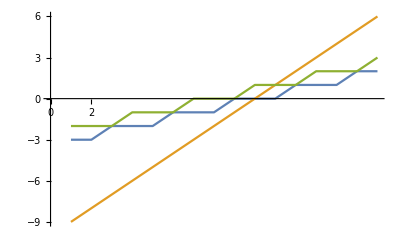

```mathematica
ListPlot[Transpose@Table[{⌊(i+1)/3⌋,i,⌈(i+1)/3⌉},{i,-9,6}],Joined->True,Ticks->{ Range[-6,3], Automatic},AxesOrigin->{0,0}]
```

```mathematica
FindSequenceFunction[{{0,1},{1,1},{2,1},{3,2},{3,3},{4,3}}]
```

FindSequenceFunction[{{0,1},{1,1},{2,1},{3,2},{3,3},{4,3}}]

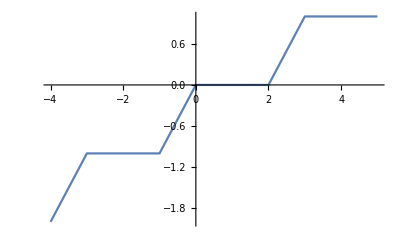

```mathematica
ListPlot[{{-4,-2},{-3,-1},{-2,-1},{-1,-1},{0,0},{1,0},{2,0},{3,1},{4,1},{5,1}},Joined->True]
```

```mathematica
planets=ResourceData@ResourceObject["Sample Data: Solar System Planets and Moons"]
```

```mathematica
planets[Keys]
```

```mathematica
planets[Values]
```

```mathematica
planets[All,Keys]
```

```mathematica
naturalUnitsData[All,All,Keys]
```

```mathematica
naturalUnitsData[Keys]
```

```mathematica
naturalUnitsData[All,Keys]
```

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Source/Reference Citation

NIST SI Brochure.

The URL string has a leading space which needs to be removed. The URL should end with .pdf instead of .pd for the URL to open the correct document.

I removed the leading space and updated the link to end in .pdf

### Detailed Source Information

#### Author/Creator

Author Name

#### Source Title

Published Title

#### Source Date

Original Publication Date

#### Source Publisher

Original Publication

#### Geographic Coverage

Area

#### Temporal Coverage

Timespan

#### Source Language

Language

#### Rights

Data Rights

### Links

Link to other related material

### Keywords

metrology

### Categories

Agriculture
 Computer Systems
 Economics
 Geometry Data
 Healthcare
 Language
 Mathematics
 Politics
 Statistics |  Astronomy
 Culture
 Education
 Government
 History
 Life Science
 Medicine
 Reference
 Text & Literature |  Chemistry
 Demographics
 Engineering
 Graphics
 Human Activities
 Machine Learning
 Meteorology
 Social Media
 Transportation |  Computational Universe
 Earth Science
 Geography
 Health
 Images
 Manufacturing
 Physical Sciences
 Sociology

### Content Types

Audio
 Graphs
 Text |  Entity Store
 Image
 Time Series |  Geospatial Data
 Numerical Data
 Video

Please select a Content Type.

I selected text and numerical data types.

### Related Resource Objects

PlanckUnitConversion

### Related Symbols

UnitSimplify

NondimensionalizationTransform

## Author Notes

Additional information about data limitations, improvements, etc.

## Submission Notes

I plan to add more documentation examples in the future. I added Mathematics as a category because it could be helpful for dimensional analysis. I had a technical issue where  wouldn’t work when I ran the code so I deployed in the cloud and used ResourceObject[
CloudObject[
 “https://www.wolframcloud.com/obj/burbery1/DeployedResources/Data/SI-\
Brochure-Data”]] instead.